```mathematica
(* calcolo curva gerarchica secondo livello dopo linearizzazione in b1 *)
f[L_,b2_,b1_] = Tanh[b2*L] + b1*(1-Tanh[b2*L]^2)*L
g[L_,b2_,b1_]=FullSimplify[D[f[L,b2,b1], L]]
```

Tanh[b2 L]+b1 L (1-Tanh[b2 L]^2)

Sech[b2 L]^2 (b1+b2-2 b1 b2 L Tanh[b2 L])

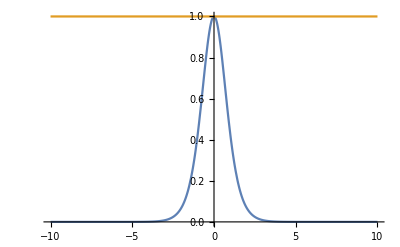

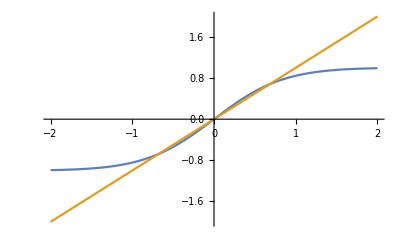

```mathematica
Plot[{g[L,0.9,0.1],1}, {L,-10,10}]
Plot[{f[L,1,0.2],L},{L,-2,2}]
```

```mathematica
(* qui x = Tanh[b2*L], è l'eq f'(L) = 1 *)
Reduce[x^3*(2*b1*b2*L== 0 && -1≤ x≤1 , x]
```